```mathematica
clear
```

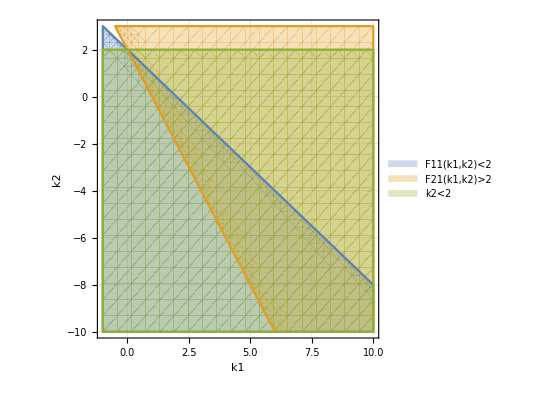

```mathematica
F11[k1_,k2_] := k1+k2
F21[k1_,k2_] := 2 k1 + k2

RegionPlot[{F11[k1,k2]<2,F21[k1,k2]>2,k2<2},{k1,-1,10},{k2,-10,3},PlotLegends->"Expressions",GridLines->Automatic,Axes->True,AxesLabel->{"k1","k2"}]
```